## Mathematical Music

I first considered the connection between math and music when I was listening to the song “No Money” by Galantis. It’s a fascinating song with many different instruments and a touch of something electronic as well, and I was curious if I could somehow represent the song in a different way. Being a mathematician, I naturally tried to use equations and expressions to represent the song, and so began my journey in the realm of mathematical music.

Mathematical music is a broad term and has varying meanings to people. It’s most commonly viewed as the math behind frequency, pitch, rhythm, and other facets of music, such as how chords of prime numbers (2nd, 3rd, 5th, and 7th) sound instinctively right for musicians. However, I was interested in something different: what mathematical equation represents the melody of a song? If I had an equation, could I turn that into a piece of music?

### The General Plan

Before I could start coming up with a solution, I had to determine precisely what I was trying to find. While I was trying to find the connection between math and music, it is important to note that I was pursuing this connection only one way— turning a given equation into a song. The corresponding connection would be to find an equation given a song, but that was not my goal in this part of the project.

My general plan was to find the values of an equation at certain points and then convert these values into notes. For example, if I was looking at the function y = x, then at every integer value of x from 1 to 10, the melody would be comprised of notes with number values from 1 to 10. However, this presented a problem immediately: the range of functions.

There were only so many notes that I could use, but some equations went on to infinity (such as quadratic equations) while others were periodic with ranges beyond possible notes (such as sin functions with large amplitudes). And so, I split my solution into two cases and came up with slightly separate ways of dealing with each type of function.

### Case 1: Functions with an Infinite Range

My first case included all functions that had an infinite range. It didn’t matter if it went to positive or negative infinity— if the function increased/decreased without limit, then it was considered in this case. To determine whether a function had an infinite range, I used the functions MaxValue and MinValue. I used these functions with an if statement to determine if a function had an infinite range, and put it all inside a custom function, which I named range.

Determining if a function had an infinite range with my range function:

```mathematica
range[f_]:=If[MaxValue[f,x]==Infinity||MinValue[f,x]==-Infinity,True,False]
```

Testing it out on some functions, we see it works as intended:

```mathematica
range[x^4]
```

True

```mathematica
range[Sin[x]]
```

False

Once I could determine if a function was infinite, I needed to find a way to express these infinite notes as values. My solution was to place a cap on the function’s values. After experimenting with number values for notes in the SoundNote function, I determined that a reasonable range was between -30 and +30, which meant I had to limit the values of these functions to be between negative and positive 30. And so, I created the value function to find the values of the function for notes. Essentially, if the function’s value was below -30, I set it to -30, and if it was above +30, I set it to +30. If it was between -30 and +30, I set the note value to be the floor of the function’s value (since SoundNote only accepted integers).

What exactly is the note value? To explain it best, think of the notes on a piano. Reduce the 88 keys to a reasonable range (which I took as 60 notes). Imagine middle C (C4) as 0, and for every half-step up, increase the note value by 1. In that sense, the note value for D# is 3. For every half-step down, decrease the note value by 1. In that sense, the note value for B is -1. With a range of -30 to +30, the notes go from F#1 to F#6, a range of 5 octaves.

Using the value function to change a function’s values into usable note values:

```mathematica
value[x_]:=Which[x<-30,-30,x>30,30,NumberQ[x],Floor[x]]
```

We can see this function working as intended after testing it out on a quadratic function.

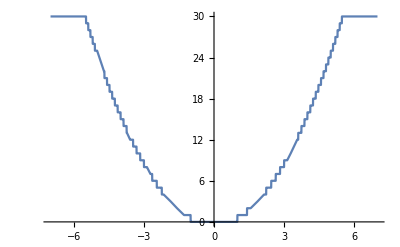

```mathematica
Plot[value[x^2],{x,-7,7}]
```

```mathematica
notes=Table[value[x^2],{x,-7,7,.5}]
```

{30,30,30,30,25,20,16,12,9,6,4,2,1,0,0,0,1,2,4,6,9,12,16,20,25,30,30,30,30}

As shown above, the note values for the function y = x^2 from -7 to +7 (with a step of .5) are bounded at +30.

Once I had a list of notes, it was trivial to simply play each of these notes with Sound after setting each note to play for .25 seconds.

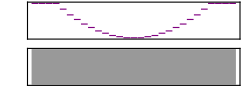

```mathematica
Sound[SoundNote[#,.25]&/@notes]
```

I noticed that the shape of the notes were very similar to the quadratic function, which was exactly what I wanted. However, this didn’t feel right to me. The function y = x^2 doesn’t grow linearly— rather it increases faster as it grows farther from the origin. This meant the tempo of these notes was off.

I experimented with many different things in order to reach the right timing for the music, such as using the x-coordinate of each note as it’s tempo or making the tempo a factor of the note values. I’ve included the some of my experiments below.

Experiment 1—directly scaling the tempo by the note values:

```mathematica
time1=notes*.5/10;
If[#==0,0.01,#]&/@time1;
experiment1={};
For[i=1,i<=Length[notes],i++,experiment1=Append[experiment1,SoundNote[notes[[i]],time1[[i]]]]];
```

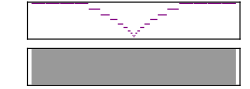

```mathematica
Sound[experiment1]
```

Experiment 2—inversely scaling the tempo by the note values:

```mathematica
time2=((1+.5)-(notes/Max[notes]))*.5;
experiment2={};
For[i=1,i<=Length[notes],i++,experiment2=Append[experiment2,SoundNote[notes[[i]],time2[[i]]]]];
```

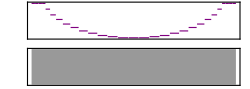

```mathematica
Sound[experiment2]
```

However, after listening to each experiment, the tempo still didn’t feel naturally correct. I puzzled over finding the appropriate tempo for several days before it hit me— the derivative. The derivative represents how fast a function is changing at a certain point in time. What better mathematical concept is there to represent the length of a note?

Specifically, if a note had a large derivative (which meant it changed really fast), I assigned it a longer length. How does this work? Well, the derivative can be seen as the instantaneous rise over run (change in y over change in x) at a particular point. In other words, a large derivative means that at that point, the function is traveling a large “distance” in an infinitesimally small amount of time. Therefore, a note with a large derivative had a longer length because it was “traveling” a large interval to get to the next note. While it was rather counterintuitive, this understanding made the music sound better and avoided some nasty code, so I took it as a win-win scenario.

To achieve the correct timing, I found the derivative of the function y = x^2 at each note position and assigned that as the timing. For example, the derivative of that function is 2x, so the note found from the position x = 7 should be held for 2*7 = 14 seconds. Obviously, I had to scale the timing down significantly (specifically, by the longest note) because 14 seconds is far too long, but the principal idea remained.

Using the derivative of the function as the timing for each note:

```mathematica
function[x_]:=x^2
dtime=Abs/@Table[function'[x],{x,-7,7,.5}];
dtime=Abs/@(dtime/Max[dtime]);
```

Keeping track of timing continuously:

```mathematica
time={0};
For[i=1,i<=Length[dtime],i++,time=Append[time,dtime[[i]]+time[[i]]]]
```

Combining the notes and the timing together:

```mathematica
finalsong={};
For[i=1,i<=Length[notes],i++,finalsong=Append[finalsong,SoundNote[notes[[i]],{time[[i]],time[[i+1]]}]]];
```

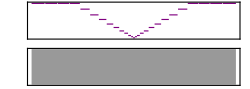

```mathematica
Sound[finalsong]
```

While it doesn’t look exactly like a quadratic function, the notes and the timing were mathematically correct, and the song sounded natural for the first time.

### Case 2: Functions with a Finite Range

Now that I had a solution for functions that went to positive or negative infinity, I turned my attention to functions with a finite range, such as sin functions. These functions returned false when checked for an infinite range with the range function.

```mathematica
range[Sin[x]]
```

False

However, since the functions in this case had finite ranges, the note values needed to be calculated differently. Specifically, I found the actual range of the function and scaled it to the range of the note values, which went from -30 to +30. For example, a standard sin function with a range from -1 to +1 would have every value multiplied by 30 in order to reach the same -30 to +30 range of the note values.

Calculating the scaled range of the sin function:

```mathematica
f=Sin[x];
scale=60/(MaxValue[f,x]-MinValue[f,x]);
```

Here’s the range of note values with and without the scale:

Without the scale:

```mathematica
n1=Table[Floor[Sin[x]],{x,-7,7,0.5}]
```

{-1,-1,0,0,0,0,0,0,-1,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,-1,-1,-1,-1,-1,-1,0,0}

With the scale:

```mathematica
n2=Table[Floor[scale*Sin[x]],{x,-7,7,0.5}]
```

{-20,-7,8,21,28,29,22,10,-5,-18,-28,-30,-26,-15,0,14,25,29,27,17,4,-11,-23,-30,-29,-22,-9,6,19}

Seeing the difference between the graphs:

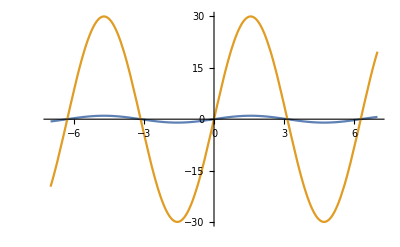

```mathematica
Plot[{Sin[x],scale*Sin[x]},{x,-7,7}]
```

Clearly, the scale was quite useful in broadening and shrinking the range of these finite functions, so as to achieve a more precise range for the note values.

Once I had the note values, I found the derivative in much the same way as before and combined the notes and the timing to achieve a rather nice melody for the sin function.

Using the derivative to find the timing of the notes:

```mathematica
function[x_]:=Sin[x]
dtime=scale*(Abs/@Table[function'[x],{x,-7,7,.5}]);
dtime=Abs/@(dtime/Max[dtime]);
```

Keeping track of timing continuously:

```mathematica
time={0};
For[i=1,i<=Length[dtime],i++,time=Append[time,dtime[[i]]+time[[i]]]]
```

Combining the notes and the timing together:

```mathematica
finalsong={};
For[i=1,i<=Length[notes],i++,finalsong=Append[finalsong,SoundNote[n2[[i]],{time[[i]],time[[i+1]]}]]];
```

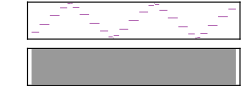

```mathematica
Sound[finalsong]
```

The above music looks very similar to the sin graph, though the notes at the peaks and troughs change rather rapidly. Again, since the notes don’t “travel” very far at these positions, they play very quickly, while the notes at the center are held for longer because they “travel” a longer interval.

Ultimately, we now have the appropriate models to find a melody for a given equation. The next step is to put them all together into one function.

### Creating a Final Model

The first step is to determine the range of the function: whether it’s infinite or finite.

```mathematica
range[f_]:=If[MaxValue[f,x]==Infinity || MinValue[f,x]==-Infinity,True,False]
```

If it has an infinite range, we take the floor function in order to isolate integers for notes and set bounds of -30 and +30.

```mathematica
value[x_]:=Which[x<-30,-30,x>30,30,True,Floor[x]]
```

If it has a finite range, we determine the scale with the minimum and maximum of the function over the desired interval.

```mathematica
scale:=60/(MaxValue[f,x ]-MinValue[f,x])
```

Then, given a function, we execute these functions over a particular range with a particular step in order to get a set of notes.

```mathematica
notevalues[f_, low_, high_, step_]:=Table[value[f],{x,low,high,step}]
```

We find the length of each note as the derivative at that point, and add them all up to have continuous timing.

```mathematica
timing[f_]:=Module[{dtime,time={0}},
dtime=Abs/@Table[f'[x],{x,-7,7,.5}];
dtime=Abs/@(dtime/Max[dtime]);
For[i=1,i<=Length[dtime],i++,time=Append[time,dtime[[i]]+time[[i]]]]]
```

We need to play the notes for their respective length of time, so we combine notes and time into a final list of SoundNotes— which are then combined into a Sound.

```mathematica
melody={};
For[i=1,i<=Length[notes],i++,melody=Append[melody,SoundNote[notes[[i]],{time[[i]],time[[i+1]]}]]]
Sound[melody];
```

Combining all of this, we end up with the function below.

```mathematica
range[f_]:=If[MaxValue[f,x]==Infinity || MinValue[f,x]==-Infinity,True,False]
value[x_]:=Which[x<-30,-30,x>30,30,NumberQ[x],Floor[x]]

MathtoMusicTransform[f_,low_,high_,step_]:=Module[{notes={},beats={},time={0},staff={}},
If[range[f]==True,notes=Table[value[N[f]],{x,low,high,step}],Module[{scale},
scale=(60/(MaxValue[f,x ]-MinValue[f,x]));
notes=Table[Floor[scale*f],{x,-10,10,1}]]];
beats=Abs/@Table[D[f,x]/.x->r,{r,low,high,step}];
beats=Abs/@(beats/Max[beats]);
For[i=1,i<=Length[beats],i++,time=Append[time,beats[[i]]+time[[i]]]];
For[i=1,i<=Length[notes],i++,staff=Append[staff,SoundNote[notes[[i]],{time[[i]],time[[i+1]]}]]];
Sound[staff]]
```

We can now test out this function on several mathematical equations.

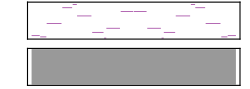

```mathematica
MathtoMusicTransform[Cos[x],-10,10,1]
```

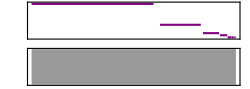

```mathematica
MathtoMusicTransform[(50000/x^5),5,14,1]
```

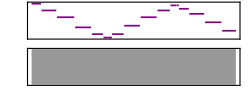

```mathematica
MathtoMusicTransform[(12/(E^x)+10Sin[x]),2,10,.5]
```

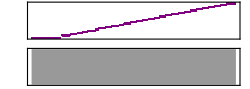

```mathematica
MathtoMusicTransform[Sqrt[x],1.,1000,10]
```

### Combining Melodies

Once MathtoMusicTransform was working for one melody, I worked on combining melodies. What would a cubic function and a cosine function sound like if they were played together? What about playing an exponential and a logarithmic function simultaneously?

There were two ways of combining melodies. One option was to literally add the note values together for the two functions and play one melody that was an amalgamation of the two given. Another option was to literally play both melodies at the same time.

I started with the first option and tried to combine a quadratic and sin function. I created the notes for the quadratic equation (y = x^2) and the sin function (sin(x)) and simply added them together and scaled the resulting notes appropriately.

Adding the note values for the quadratic and sin functions together:

```mathematica
scale=(60/(MaxValue[Sin[x],x]-MinValue[Sin[x],x]));
quadnotes=Table[value[x^2],{x,-7,7,.5}];
sinnotes=Table[Floor[scale*Sin[x]],{x,-7,7,0.5}];

finalnotes=quadnotes+sinnotes;
finalnotes=Floor[If[Max[finalnotes]>30||Min[finalnotes]<-30,finalnotes*=30/Max[finalnotes],finalnotes]];
```

I then played them with a standard length of .25 seconds per note, just to see what the result looked like.

```mathematica
Sound[SoundNote[#,.25]&/@f]
```

Sound[Sin[SoundNote[x,0.25]]]

The note graph looks like an amalgamation of a quadratic and sin function, with the peaks and troughs of a sin function and the growth to infinity at the ends. It also sounds somewhat like a combination of the sin and quadratic functions, though that likely varies from person to person.

The second option was to play both melodies at the same time, which meant I needed to make each melody (for a quadratic and sin function) separately and then join the two melodies inside the Sound function at the very end.

Creating separate melodies for the quadratic and sin function:

```mathematica
quad[x_]:=x^2
quadnotes=Table[value[x^2],{x,-7,7,.5}];
quadtime=Table[quad'[x],{x,-7,7,.5}];
quadtime=Abs/@(quadtime/Max[quadtime]);
quadt={0};
For[i=1,i<=Length[quadtime],i++,quadt=Append[quadt,quadtime[[i]]+quadt[[i]]]];
qtotal={};
For[i=1,i<=Length[quadnotes],i++,qtotal=Append[qtotal,SoundNote[quadnotes[[i]],{quadt[[i]],quadt[[i+1]]}]]];

sin[x_]:=Sin[x]
sinnotes=Table[Floor[scale*Sin[x]],{x,-7,7,0.5}];
sintime=Table[sin'[x],{x,-7,7,.5}];
sintime=Abs/@(sintime/Max[sintime]);
sint={0};
For[i=1,i<=Length[sinnotes],i++,sint=Append[sint,sintime[[i]]+sint[[i]]]];
stotal={};
For[i=1,i<=Length[sinnotes],i++,stotal=Append[stotal,SoundNote[sinnotes[[i]],{sint[[i]],sint[[i+1]]}]]];
```

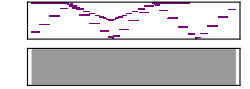

```mathematica
Sound[Join[qtotal,stotal]]
```

The melody is pretty discordant, but the individual note graphs of a quadratic and sin function are distinctive. The combination note graph also mimics the graph of a quadratic and sin function, as seen below, though the scaling is very different. Furthermore, it’s a lot easier to pick out the individual notes for each melody when they’ve been combined in this manner.

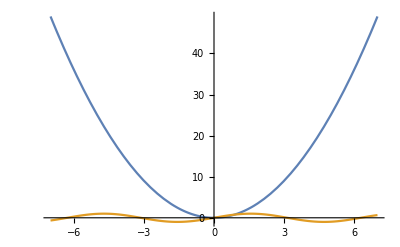

```mathematica
Plot[{x^2,Sin[x]},{x,-7,7}]
```

Here’s what an exponential (e^x) and logarithmic (ln(x)) function sound like and look like together:

```mathematica
exp[x_]:=E^x
expnotes=Table[value[E^x],{x,-4,5,.25}];
exptime=Table[exp'[x],{x,-4,5,.25}];
exptime=Abs/@(exptime/Max[exptime]);
expt={0};
For[i=1,i<=Length[expnotes],i++,expt=Append[expt,exptime[[i]]+expt[[i]]]];
etotal={};
For[i=1,i<=Length[expnotes],i++,etotal=Append[etotal,SoundNote[expnotes[[i]],{expt[[i]],expt[[i+1]]}]]];

log[x_]:=Log[x]
lognotes=Table[value[Log[x]],{x,.5,14,.5}];
logtime=Table[log'[x],{x,.5,14,.5}];
logtime=Abs/@(logtime/Max[logtime]);
logt={0};
For[i=1,i<=Length[lognotes],i++,logt=Append[logt,logtime[[i]]+logt[[i]]]];
ltotal={};
For[i=1,i<=Length[lognotes],i++,ltotal=Append[ltotal,SoundNote[lognotes[[i]],{logt[[i]],logt[[i+1]]}]]];
```

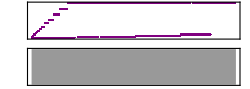

```mathematica
Sound[Join[etotal,ltotal]]
```

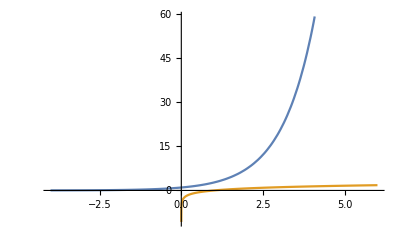

```mathematica
Plot[{E^x,Log[x]},{x,-4,6}]
```

### Future Work

This was definitely a really interesting project to work on, and I think there’s much more potential in this interpretation of mathematical music. Specifically, I’m curious to see if I can solve this problem in the opposite direction: creating a function to describe a given melody. I’d be interested in using Fourier Transforms to try to do that!

Beyond that, there are many other interpretations of mathematical music and I’d love to see what the community creates.

And of course, special thanks to Zach Shelton with his help in making this project possible.